# Finite state machine

## Finite Automata

DFA/NFA common functions

```mathematica
Protect[ϵ]; (* ϵ will be used as a symbol to denote the empty string *)
Transition[parent_,child_,inputSymbol_]:=<|"Parent"->parent,"Node"->child,"InputSymbol"->inputSymbol|>;
EmptyTransition[parent_,child_]:=Transition[parent,child,ϵ];
FATransitions[transitions_,state_]:=Cases[transitions,KeyValuePattern[{"Parent"->state}]];
Concatenate[l_]:=Apply[Join,l];
```

Plotting functions

```mathematica
NameTag[machine_Association,state_]:=Subscript[machine["Name"],ToString[state]];

Options[FAPlot]={"Legended"->True,"Labeled"->False};
FAPlot[machine_Association,OptionsPattern[]]:=Block[{graphData,startTag,acceptTags,legend,graph},
Switch[OptionValue["Labeled"],
True,
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[p->n,i]];
startTag = machine["StartState"]->Red;
acceptTags = Map[If[# ≠ machine["StartState"],#->Green,#->Purple]&,machine["AcceptStates"]];
,
False,
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>p->n];
startTag = machine["StartState"]->Red;
acceptTags = Map[If[# ≠ machine["StartState"],#->Green,#->Purple]&,machine["AcceptStates"]];
];

legend = PointLegend[{LightBlue,Red,Green,Purple},{"State","Start state","Accept state","Start/Accept state"},LegendMarkers->Graphics[Disk[]]];

graph = Graph[
graphData,
ImageSize->400,
VertexLabels->"Name",
VertexStyle->Join[{startTag},acceptTags],
VertexSize->0.1
];

If[OptionValue["Legended"],
Return[Legended[graph,legend]],
Return[graph]
]
];
```

Deterministic Finite Automata (DFA)

```mathematica
(* DFA object constructor *)
DFA[name_,transitions_,start_,accept_,stateExpr_:{}]:=
<|
"Name"->name,(* Descriptive name to keep in track the regular operations applied to it *)
"Type"->"DFA",
"Transitions"->transitions,
"StartState"->start,
"AcceptStates"->accept,
"StateExpressions"->stateExpr (* Each state may have an associated expression *)
|>;

(* Return every deterministic transition leading to state *)
DFATransitions[transitions_,state_]:=Cases[transitions,KeyValuePattern[{"Parent"->state}]];

(* Get the next state *)
Options[DFAIterate]={"Trace"->False};
DFAIterate[transitions_,state_,inputSymbol_,OptionsPattern[]]:=Block[{next},
next = Cases[
DFATransitions[transitions,state],
KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]
];

(* A DFA must have only one available transition *)
If[Length[next]==1,
If[OptionValue["Trace"],
Return[First[next]]
,
Return[First[next]["Node"]];
]
,
Print["Error: Nondeterminism found"];
Return[$Failed];
]
];

(* Returns the trace of the computation and the result of whether the machine accepts the inputString *)
DFACompute[machine_Association,inputString_]:=Block[{computation,result},
computation = FoldList[
DFAIterate[machine["Transitions"],#1["Node"],#2,"Trace"->True]&,
<|"Node"->machine["StartState"]|>,
inputString
];
result = MemberQ[machine["AcceptStates"],Last[computation]["Node"]];
Return[{computation,result}]
];
```

Plotting functions

```mathematica
Options[DFAPlotExecution] = {"SimpleNodes"->False};
DFAPlotExecution[machine_Association,inputString_,OptionsPattern[]]:=DynamicModule[{trace,executionSteps,ruleIndexes,graphData,startTag,acceptTags},
trace = DFACompute[machine,inputString];
executionSteps = Drop[First[trace],1];
ruleIndexes = Map[Position[machine["Transitions"],#]&,executionSteps];

If[OptionValue["SimpleNodes"],
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[p->n,i]];
startTag = machine["StartState"]->Red;
acceptTags = Map[#->Green&,machine["AcceptStates"]];
,
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[NameTag[machine,p]->NameTag[machine,n],i]];
startTag = NameTag[machine,machine["StartState"]]->Red;
acceptTags = Map[NameTag[machine,#]->Green&,machine["AcceptStates"]];
];

Manipulate[
Column[
{
Row[{"Input string: ",Grid[{inputString},Frame->All,Background->{i->Green}]}],
Row[{"Result: ",If[Last[trace],"Accepted","Not accepted"]}],
Graph[
MapAt[Style[#,Red]&,graphData,ruleIndexes[[i]]],
ImageSize->400,
VertexLabels->"Name",
VertexStyle->Join[{startTag},acceptTags],
VertexSize->0.1
]
}
]
,
{i,1,Length[ruleIndexes],1}
]
];
```

DFA declaration, where L(m_1) = {ω | ω contains at least one 1 and an even number of 0s follow the last 1}.

```mathematica
m1 = DFA[
"q",
{
Transition[1,1,{0}],
Transition[1,2,{1}],
Transition[2,2,{1}],
Transition[2,3,{0}],
Transition[3,2,{0,1}]
},
1,
{2}
]
```

<|Name→q,Type→DFA,Transitions→{<|Parent→1,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→3,InputSymbol→{0}|>,<|Parent→3,Node→2,InputSymbol→{0,1}|>},StartState→1,AcceptStates→{2},StateExpressions→{}|>

Plot of m_1

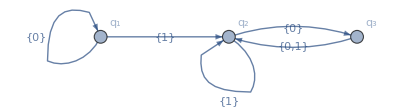

```mathematica
FAPlot[m1]
```

Trace of the computation

```mathematica
DFACompute[m1,{1,0,1,0,0}]
```

{{<|Node→1|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→3,InputSymbol→{0}|>,<|Parent→3,Node→2,InputSymbol→{0,1}|>,<|Parent→2,Node→3,InputSymbol→{0}|>,<|Parent→3,Node→2,InputSymbol→{0,1}|>},True}

Plot of the execution with 10100 as input

```mathematica
DFAPlotExecution[m1,{1,0,1,0,0}]
```

```mathematica
DFAPlotExecution[m1,{1,0,1,0,1,0,0}]
```

```mathematica
DFAPlotExecution[m1,{1,0,1,1,1,0,1,0}]
```

DFA declaration, where L(m_2) = {ω | ω ends in a 1}.

```mathematica
m2 = DFA[
"q",
{
Transition[1,1,{0}],
Transition[1,2,{1}],
Transition[2,2,{1}],
Transition[2,1,{0}]
},
1,
{2}
]
```

<|Name→q,Type→DFA,Transitions→{<|Parent→1,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→1,InputSymbol→{0}|>},StartState→1,AcceptStates→{2},StateExpressions→{}|>

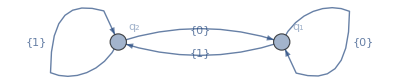

```mathematica
FAPlot[m2]
```

```mathematica
DFACompute[m2,{1,0,1,0,0}]
```

{{<|Node→1|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→1,InputSymbol→{0}|>},False}

```mathematica
DFAPlotExecution[m2,{1,1,1,0,1}]
```

Non-deterministic Finite Automata (NFA)

```mathematica
NFA[name_,transitions_,start_,accept_,stateExpr_:{}]:=
<|
"Name"->name,
"Type"->"NFA",
"Transitions"->transitions,
"StartState"->start,
"AcceptStates"->accept ,
"StateExpressions"->stateExpr
|>;

ContainsQ[list_List,form_]:=MemberQ[list,form];
ContainsQ[form1_,form2_]:=form1===form2;

PureNondetStateQ[transitions_,state_]:=(DeleteDuplicates[FATransitions[transitions,state][[All,"InputSymbol"]]] === {ϵ});

(* Return the list of nodes accesible via empty transitions *)
NFANondetNodes[transitions_,state_Association]:=Cases[FATransitions[transitions,state["Node"]],KeyValuePattern[{"InputSymbol"->i_/;ContainsQ[i,ϵ]}]];
NFANondetNodes[transitions_,state_Integer]:=Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;ContainsQ[i,ϵ]}]];
NFANondetNodes[transitions_,state_List]:=DeleteDuplicates[Flatten[Map[NFANondetNodes[transitions,#]&,state]]];
NFANondetNodesRecursive[transitions_,states_] := FixedPoint[DeleteDuplicates[Join[#,NFANondetNodes[transitions,#[[All,"Node"]]]]]&,states];

Options[NFAIterate]={"Trace"->False};
NFAIterate[transitions_,state_?AtomQ,inputSymbol_,OptionsPattern[]]:=Block[{next,deterministicTransitions,forkTransitions,deterministicNodes,emptyTransition},
(* Get all the transitions corresponding to a DFA *)
deterministicTransitions = Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]];
deterministicNodes = Sort[DeleteDuplicates[deterministicTransitions[[All,"Node"]]]];

(* Run through the empty transitions of the DFA nodes *)
forkTransitions = NFANondetNodes[transitions,deterministicNodes]; (* Get past the current deterministic nodes *)
forkTransitions = NFANondetNodesRecursive[transitions,forkTransitions]; (* Append every valid nondet transition *)

(* The next nodes will be a union between the deterministic transitions and the nodes reachable from nondet transitions *)
next = DeleteDuplicates[Join[deterministicTransitions,forkTransitions]];

If[Length[next]>0,
If[OptionValue["Trace"],
Return[next],
Return[next[[All,"Node"]]]
]
,
Return[{}]
];
];
NFAIterate[transitions_,state_List,inputSymbol_,opt:OptionsPattern[]]:=DeleteDuplicates[Flatten[Map[NFAIterate[transitions,#,inputSymbol,opt]&,state]]];

NFACompute[machine_Association,inputString_]:=Block[{computation,result,start},
start = NFANondetNodesRecursive[
machine["Transitions"],
{<|"Node"->machine["StartState"]|>}
];
computation = FoldList[
NFAIterate[machine["Transitions"],#1[[All,"Node"]],#2,"Trace"->True]&,
start,
inputString
];
result = Apply[Or,Map[MemberQ[machine["AcceptStates"],#]&,Last[computation][[All,"Node"]]]];
Return[{computation,result}];
];
```

Plotting functions

```mathematica
(* Pretty output for NFAExecutionTree *)
GenerationTransform[node_Association,generation_]:={
StringJoin["G: ",ToString[generation-1]," S: ",ToString[node["Parent"]]]->StringJoin["G: ",ToString[generation]," S: ",ToString[node["Node"]]]
,
ToString[node["InputSymbol"]]
};
GenerationTransform[nodes_List,generation_]:=Map[GenerationTransform[#,generation]&,nodes];

NFAReplaceParents[transitions_,newParent_]:=Map[MapAt[newParent&,#,Key["Parent"]]&,transitions];

NFAExecutionTreeIterate[transitions_,state_?AtomQ,inputSymbol_]:=Block[{next,deterministicTransitions,forkTransitions,deterministicNodes,emptyTransition},
deterministicTransitions = Cases[FATransitions[transitions,state],KeyValuePattern[{"InputSymbol"->i_/;MemberQ[i,inputSymbol]}]];
deterministicNodes = Sort[DeleteDuplicates[deterministicTransitions[[All,"Node"]]]];

forkTransitions = NFANondetNodes[transitions,deterministicNodes];
forkTransitions = NFANondetNodesRecursive[transitions,forkTransitions];
forkTransitions = NFAReplaceParents[forkTransitions,state]; (* This is the only difference from NFAIterate *)

next = DeleteDuplicates[Join[deterministicTransitions,forkTransitions]];

If[Length[next]>0,Return[next],Return[{}]];
];
NFAExecutionTreeIterate[transitions_,state_List,inputSymbol_]:=DeleteDuplicates[Flatten[Map[NFAExecutionTreeIterate[transitions,#,inputSymbol]&,state]]];

NFAExecutionTreeComputeTrace[machine_Association,inputString_]:=Block[{computation,result,start},
start = NFANondetNodesRecursive[machine["Transitions"],{<|"Node"->machine["StartState"]|>}]; (* This is the only difference from NFACompute *)
computation = FoldList[NFAExecutionTreeIterate[machine["Transitions"],#1[[All,"Node"]],#2]&,start,inputString];
result = Apply[Or,Map[MemberQ[machine["AcceptStates"],#]&,Last[computation][[All,"Node"]]]];
Return[{computation,result}];
];

(* Plot the execution tree showing the active states at every input *)
NFAExecutionTree[machine_Association,inputString_]:=Block[{trace,root,traceTree},
trace = Drop[First[NFAExecutionTreeComputeTrace[machine,inputString]],1];
root = First[GenerationTransform[First[trace],1]];
traceTree = Flatten[MapIndexed[GenerationTransform[#1,First[#2]]&,trace],1];

TreePlot[
DeleteDuplicates[traceTree],
Automatic,StringJoin["G: 0 S: ",ToString[machine["StartState"]]],

VertexLabeling->True,
DirectedEdges->True
]
];

Options[NFAPlotExecution] = {"SimpleNodes"->False};
NFAPlotExecution[machine_Association,inputString_,OptionsPattern[]]:=DynamicModule[{trace,executionSteps,ruleIndexes,graphData,startTag,acceptTags,currentStates,start,parentStates},
trace = NFACompute[machine,inputString];
executionSteps = First[trace];
ruleIndexes = Map[Position[machine["Transitions"],Apply[Alternatives,#]]&,executionSteps];
currentStates = Cases[machine["Transitions"],KeyValuePattern[{"Node"->n_}]:>n];
parentStates = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_}]:>p];
start = DeleteDuplicates[Sort[Join[{<|"Node"->machine["StartState"]|>},NFANondetNodes[machine["Transitions"],machine["StartState"]]]]];

If[OptionValue["SimpleNodes"],
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[p->n,i]];
acceptTags = Map[#->Green&,machine["AcceptStates"]];
startTag = machine["StartState"]->Red;
,
graphData = Cases[machine["Transitions"],KeyValuePattern[{"Parent"->p_,"Node"->n_,"InputSymbol"->i_}]:>Labeled[NameTag[machine,p]->NameTag[machine,n],i]];
acceptTags = Map[NameTag[machine,#]->Green&,machine["AcceptStates"]];
startTag = NameTag[machine,machine["StartState"]]->Red;
];

Manipulate[
Column[
{
Row[{"Input string: ",Grid[{inputString},Frame->All,Background->{(i-1)->Green}]}],
Row[{"Start states: ",Sort[start[[All,"Node"]]]}],
Row[{"Parent states: ",Sort[Extract[parentStates,ruleIndexes[[i]]]]}],
Row[{"Current states: ",Sort[Extract[currentStates,ruleIndexes[[i]]]]}],
Row[{"Accept states: ",machine["AcceptStates"]}],
Row[{"Result: ",If[Last[trace],"Accepted","Not accepted"]}],
Graph[
MapAt[Style[#,Red]&,graphData,ruleIndexes[[i]]],
ImageSize->400,
VertexLabels->"Name",
VertexStyle->Join[{startTag},acceptTags],
VertexSize->0.1
]
}
]
,
{i,1,Length[ruleIndexes],1}
]
];
```

NFA declaration, where L(n_1) = {ω | ω contains either 101 or 11 as a substring}.

```mathematica
n1 = NFA[
"q",
{
Transition[1,1,{0,1}],
Transition[1,2,{1}],
Transition[2,3,{0,ϵ}],
Transition[3,4,{1}],
Transition[4,4,{0,1}]
},
1,
{4}
]
```

<|Name→q,Type→NFA,Transitions→{<|Parent→1,Node→1,InputSymbol→{0,1}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→3,InputSymbol→{0,ϵ}|>,<|Parent→3,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→4,InputSymbol→{0,1}|>},StartState→1,AcceptStates→{4},StateExpressions→{}|>

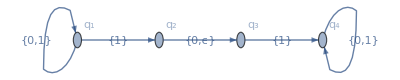

```mathematica
FAPlot[n1]
```

```mathematica
Column@First[NFACompute[n1,{0,1,0,1,1,0}]][[All,All,"Node"]]
```

{1}
{1}
{1,2,3}
{1,3}
{1,2,3,4}
{1,2,3,4,4}
{1,3,4}

```mathematica
NFAPlotExecution[n1,{0,1,0,1,1,0}]
```

```mathematica
NFAPlotExecution[n1,{1,0,0,1,0,0,1}]
```

```mathematica
NFAPlotExecution[n1,{1,0,1,0,1,1}]
```

```mathematica
NFAExecutionTree[n1,{0,1,0,1,1,0}]
```

NFA declaration, where L(nfa) = 0 Σ^*1.

```mathematica
nfa = NFA[
"q",
{
Transition[0,1,{0}],
EmptyTransition[1,2],
EmptyTransition[1,3],
Transition[2,4,{1}],
EmptyTransition[4,1],
Transition[3,5,{0}],
EmptyTransition[5,1],
EmptyTransition[4,6],
EmptyTransition[5,6],
Transition[6,7,{1}]
},
0,
{7}
]
```

<|Name→q,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>,<|Parent→2,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→1,InputSymbol→ϵ|>,<|Parent→3,Node→5,InputSymbol→{0}|>,<|Parent→5,Node→1,InputSymbol→ϵ|>,<|Parent→4,Node→6,InputSymbol→ϵ|>,<|Parent→5,Node→6,InputSymbol→ϵ|>,<|Parent→6,Node→7,InputSymbol→{1}|>},StartState→0,AcceptStates→{7},StateExpressions→{}|>

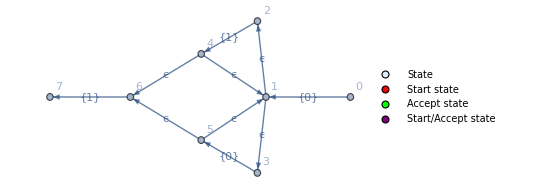

```mathematica
FAPlot[nfa]
```

```mathematica
NFACompute[nfa,{0,0,1,1,1}]
```

{{{<|Node→0|>},{<|Parent→0,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>},{<|Parent→3,Node→5,InputSymbol→{0}|>,<|Parent→5,Node→1,InputSymbol→ϵ|>,<|Parent→5,Node→6,InputSymbol→ϵ|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>},{<|Parent→6,Node→7,InputSymbol→{1}|>,<|Parent→2,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→1,InputSymbol→ϵ|>,<|Parent→4,Node→6,InputSymbol→ϵ|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>},{<|Parent→6,Node→7,InputSymbol→{1}|>,<|Parent→2,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→1,InputSymbol→ϵ|>,<|Parent→4,Node→6,InputSymbol→ϵ|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>},{<|Parent→6,Node→7,InputSymbol→{1}|>,<|Parent→2,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→1,InputSymbol→ϵ|>,<|Parent→4,Node→6,InputSymbol→ϵ|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>}},True}

```mathematica
NFAPlotExecution[nfa,{0,0,1,1,1}]
```

```mathematica
NFAExecutionTree[nfa,{0,0,1,1,1}]
```

NFA Operations

Implementation of the regular operations

```mathematica
TransitionApplyThreshold[transition_,threshold_]:=MapAt[#+threshold&,transition,{{Key["Parent"]},{Key["Node"]}}];
MachineApplyThreshold[machine_Association,threshold_]:=<|
"Name"->machine["Name"],
"Transitions"->Map[TransitionApplyThreshold[#,threshold]&,machine["Transitions"]],
"StartState"->machine["StartState"]+threshold,
"AcceptStates"->machine["AcceptStates"]+threshold,
"StateExpressions"->If[Length[machine["StateExpressions"]]≠ 0,MapAt[#+threshold&,machine["StateExpressions"],{All,1}],{}]
|>;
```

### Simplification

```mathematica
GetDirectSuccesors[machine_,state_]:=Select[
Nest[NFANondetNodes[machine["Transitions"],#]&,{state},2],
(!ContainsQ[machine["AcceptStates"],#["Parent"]] &&PureNondetStateQ[machine["Transitions"],#["Parent"]] && Length[FAParents[machine["Transitions"],#["Parent"]]]==1)
&
];

ReplaceKey[assoc_,key_,replaceTo_]:=MapAt[replaceTo&,assoc,Key[key]];

DeleteIntermediateTransition[transitions_,startState_,endState_]:=Block[{deleteState,replacement,newTransitions,cleanedUp},
deleteState = endState["Parent"];
replacement = ReplaceKey[endState,"Parent",startState["Node"]];
cleanedUp = DeleteCases[transitions,KeyValuePattern["Parent"->deleteState]];
cleanedUp = DeleteCases[cleanedUp,KeyValuePattern["Node"->deleteState]];

newTransitions = Append[cleanedUp,replacement];
Return[newTransitions];
];

SimplifyStateIteration[nfa_,state_]:=Block[{newMachine,newTransitions},
newMachine = nfa;
newTransitions = Fold[
DeleteIntermediateTransition[#1,<|"Node"->state|>,#2]&,
nfa["Transitions"],
GetDirectSuccesors[nfa,state]
];
newMachine["Transitions"] = newTransitions;
Return[newMachine];
];
SimplifyState[nfa_,state_]:=FixedPoint[SimplifyStateIteration[#,state]&,nfa];

SimplifyMachine[nfa_]:=Block[{simplified,oldStates,newStates,stateRelabelRule = {}},
simplified = Fold[SimplifyState,nfa,GetStates[nfa["Transitions"]]];

oldStates = GetStates[simplified["Transitions"]];
newStates = Range[0,Length[oldStates]-1];
stateRelabelRule = Thread[oldStates->newStates];

simplified["Transitions"] = DeleteDuplicates[ReplaceAll[simplified["Transitions"],stateRelabelRule]];
simplified["StartState"] = Replace[simplified["StartState"],stateRelabelRule];
simplified["AcceptStates"] = ReplaceAll[simplified["AcceptStates"],stateRelabelRule];
If[Length[simplified["StateExpressions"]]≠ 0,
simplified["StateExpressions"] = MapAt[Replace[#,stateRelabelRule]&,simplified["StateExpressions"],{All,1}];
];
Return[simplified];
];
```

```mathematica
abc = SimplifyMachine@RegexUnion[Regex["a"],Regex["b"],Regex["c"],Regex["d"]]
```

<|Name→a∪b∪c∪d,Type→NFA,Transitions→{<|Parent→1,Node→2,InputSymbol→{a}|>,<|Parent→3,Node→4,InputSymbol→{b}|>,<|Parent→5,Node→6,InputSymbol→{c}|>,<|Parent→7,Node→8,InputSymbol→{d}|>,<|Parent→0,Node→7,InputSymbol→ϵ|>,<|Parent→0,Node→5,InputSymbol→ϵ|>,<|Parent→0,Node→1,InputSymbol→ϵ|>,<|Parent→0,Node→3,InputSymbol→ϵ|>},StartState→0,AcceptStates→{2,4,6,8},StateExpressions→{}|>

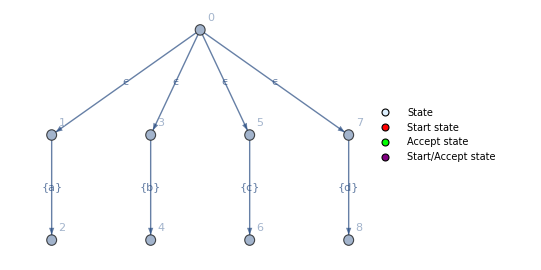

```mathematica
FAPlot[abc,"Labeled"->True]
```

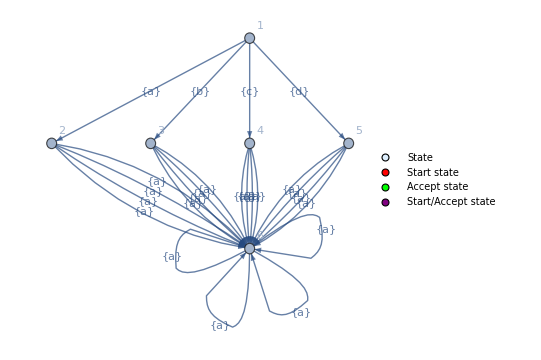

```mathematica
FAPlot[NFAToDFA[abc],"Labeled"->True]
```

```mathematica
NFACompute[nfa,{0,0,1,1,1}]
```

{{{<|Node→0|>},{<|Parent→0,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>},{<|Parent→3,Node→5,InputSymbol→{0}|>,<|Parent→5,Node→1,InputSymbol→ϵ|>,<|Parent→5,Node→6,InputSymbol→ϵ|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>},{<|Parent→6,Node→7,InputSymbol→{1}|>,<|Parent→2,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→1,InputSymbol→ϵ|>,<|Parent→4,Node→6,InputSymbol→ϵ|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>},{<|Parent→6,Node→7,InputSymbol→{1}|>,<|Parent→2,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→1,InputSymbol→ϵ|>,<|Parent→4,Node→6,InputSymbol→ϵ|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>},{<|Parent→6,Node→7,InputSymbol→{1}|>,<|Parent→2,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→1,InputSymbol→ϵ|>,<|Parent→4,Node→6,InputSymbol→ϵ|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→3,InputSymbol→ϵ|>}},True}

```mathematica
NFACompute[SimplifyMachine[nfa],{0,0,1,1,1}]
```

{{{<|Node→0|>},{<|Parent→0,Node→1,InputSymbol→{0}|>},{},{},{},{}},False}

### Union

```mathematica
NFAUnion[machine1_Association,machine2_Association]:=Block[{minIndex,newIndexThreshold,newM1,newM2,newAccept,newTransitions,newMachine,newStateExpressions},
minIndex = Min[machine1["Transitions"][[All,"Parent"]]];
newIndexThreshold = Max[machine1["Transitions"][[All,"Node"]]]+1;
newM1 = MachineApplyThreshold[machine1,1];
newM2 = MachineApplyThreshold[machine2,newIndexThreshold+1];
newAccept = Sort[Join[newM1["AcceptStates"],newM2["AcceptStates"]]];
newTransitions = {EmptyTransition[minIndex,newM1["StartState"]], EmptyTransition[minIndex,newM2["StartState"]]};
newStateExpressions = SortBy[Join[newM1["StateExpressions"],newM2["StateExpressions"]],First];

newMachine = <|
"Name"->StringJoin[machine1["Name"],"∪",machine2["Name"]],
"Type"->"NFA",
"Transitions"->Join[newM1["Transitions"],newM2["Transitions"],newTransitions],
"StartState"->minIndex,
"AcceptStates"->newAccept,
"StateExpressions"->newStateExpressions
|>;
Return[newMachine];
];
NFAUnion[machines__/;Length[List[machines]]>2]:=Fold[NFAUnion,First[List[machines]],Rest[List[machines]]];
```

```mathematica
FAPlot@NFAUnion[nfa,nfa]
```

### Concatenation

```mathematica
NFAConcatention[machine1_Association,machine2_Association]:=Block[{newIndexThreshold,newM2,newTransitions,newMachine,newStateExpressions},
newIndexThreshold = Max[machine1["Transitions"][[All,"Node"]]]+1;
newM2 = MachineApplyThreshold[machine2,newIndexThreshold];

newTransitions = Map[EmptyTransition[#,newM2["StartState"]]&,machine1["AcceptStates"]];

newStateExpressions = Join[machine1["StateExpressions"],newM2["StateExpressions"]];
newStateExpressions = If[Length[newStateExpressions]≠ 0,SortBy[Join[machine1["StateExpressions"],newM2["StateExpressions"]],First],{}];

newMachine = <|
"Name"->StringJoin[machine1["Name"],machine2["Name"]],
"Type"->"NFA",
"Transitions"->Join[machine1["Transitions"],newM2["Transitions"],newTransitions],
"StartState"->machine1["StartState"],
"AcceptStates"->newM2["AcceptStates"],
"StateExpressions"->newStateExpressions
|>;
Return[newMachine];
];
NFAConcatention[machines__/;Length[List[machines]]>2]:=Fold[NFAConcatention,First[List[machines]],Rest[List[machines]]];
```

```mathematica
FAPlot@NFAConcatention[nfa,nfa]
```

```mathematica
NFAConcatention[nfa,nfa]
```

### Kleene star

```mathematica
NFAStar[machine_Association]:=Block[{minIndex,newM,newTransitions,newAccept,newMachine},
minIndex = Min[machine["Transitions"][[All,"Parent"]]];
newM = MachineApplyThreshold[machine,1];
newTransitions = Join[{EmptyTransition[minIndex,newM["StartState"]]},Map[EmptyTransition[#,newM["StartState"]]&,newM["AcceptStates"]]];
newAccept = Append[newM["AcceptStates"],minIndex];

newMachine = <|
"Name"->StringJoin["(",machine["Name"],")^*"],
"Type"->"NFA",
"Transitions"->Join[newM["Transitions"],newTransitions],
"StartState"->minIndex,
"AcceptStates"->newAccept,
"StateExpressions"->newM["StateExpressions"]
|>;
Return[newMachine];
];
```

```mathematica
NFAStar[nfa]
```

```mathematica
FAPlot@NFAStar[nfa]
```

### Conversion to DFA

```mathematica
(* Check if there is at least one of the accepted states in searchState *)
ContainsStateQ[stateList_,searchState_?AtomQ]:=MemberQ[stateList,searchState];
ContainsStateQ[stateList_,searchState_List]:=Apply[Or,Map[MemberQ[stateList,#]&,searchState]];

(* Get parents of the current state *)
FAParents[transitions_,state_]:=DeleteDuplicates[Cases[transitions,KeyValuePattern[{"Node"->state}]][[All,"Parent"]]];

(* Check if the state is inaccesible *)
JunkStateQ[transitions_,start_,state_]:=Block[{stateParents,nonSelfTransitions},
If[ContainsStateQ[start,state],Return[False]];
stateParents = FAParents[transitions,state];
nonSelfTransitions = Complement[stateParents,{state}];
If[Length[nonSelfTransitions]==0,
Return[True],
Return[False]
]
];

SafeSort[l_List]:=Sort[l];
SafeSort[l_?AtomQ]:=l;

(* Infer the alphabet from the transition list *)
GetAlphabet[transitions_]:=DeleteCases[DeleteDuplicates[Flatten[transitions[[All,"InputSymbol"]]]],ϵ];

(* Infer the states from the transition list *)
GetStates[transitions_]:=Sort[DeleteDuplicates[Flatten[Cases[transitions,KeyValuePattern[{"Parent"->p_,"Node"->n_}]:>{p,n}]]]];

(* Get the states reachable from the current states list *)
Explore[transitions_,states_]:=Map[
Transition[
SafeSort[states],
SafeSort[DeleteDuplicates[NFAIterate[transitions,states,#,"Trace"->False]]],
{#}]&,
GetAlphabet[transitions]
];

(* Explore one step down each branch of the computation and append it to the explored branches list *)
StepDown[transitions_,branches_]:=DeleteDuplicates[
Flatten[
Join[
branches,
Map[
Explore[
transitions,
#["Node"]
]&,
branches
]
],
1]
];

NewStateNode[node_,newStateRules_]:=
<|
"Parent"->Replace[node["Parent"],newStateRules],
"Node"->Replace[node["Node"],newStateRules],
"InputSymbol"->node["InputSymbol"]
|>;

NFAToDFA[machine_Association]:=Block[{protoDFA,start,protoDFAStates,newStateRules,newStates,containsAccept,newMachine,newAccept,newStart,newTransitions,newTransitionsCleanedUp,protoDFAExpressionNodes,newStateExpressionsNodes},
If[machine["Type"] =!= "NFA",Return[$Failed]];

(* Explore all paths until there is no unexplored transition *)
start = 
FixedPoint[
DeleteDuplicates[
Join[
#,
NFANondetNodes[machine["Transitions"],#[[All,"Node"]]]]
]&,
{<|"Node"->machine["StartState"]|>}
];

(* Make a DFA by exploring all possible paths in the NFA *)
protoDFA = FixedPoint[StepDown[machine["Transitions"],#]&,{<|"Node"->start[[All,"Node"]]|>}];
protoDFAStates = DeleteDuplicates[Join[Drop[protoDFA,1][[All,"Parent"]],Drop[protoDFA,1][[All,"Node"]]]];

(* Match old NFA parameters to the new DFA *)
newStateRules = Thread[protoDFAStates->Range[Length[protoDFAStates]]];
newStates =newStateRules[[All,2]];
containsAccept = Position[protoDFAStates,s_/;ContainsStateQ[s,machine["AcceptStates"]]];
newAccept = Extract[newStates,containsAccept];
newStart = Replace[First[protoDFAStates],newStateRules];
newTransitions = Map[NewStateNode[#,newStateRules]&,Drop[protoDFA,1]];
newTransitionsCleanedUp = DeleteDuplicates[DeleteCases[newTransitions,t_/; JunkStateQ[newTransitions,newStart,t["Node"]]]];

protoDFAExpressionNodes = Concatenate[
Map[
Thread[Cases[protoDFAStates,s_/;ContainsStateQ[s,First[#]]]->Last[#]]&,
machine["StateExpressions"]
]
];
If[Length[protoDFAExpressionNodes]≠0,
newStateExpressionsNodes = MapAt[Replace[#,newStateRules]&,protoDFAExpressionNodes,{All,1}]
,
newStateExpressionsNodes = {}
];

newMachine = <|
"Name"->machine["Name"],
"Type"->"DFA",
"Transitions"->newTransitionsCleanedUp,
"StartState"->newStart,
"AcceptStates"->newAccept,
"StateExpressions"->newStateExpressionsNodes
|>;
Return[newMachine];
];
```

```mathematica
DFACompute[NFAToDFA[n1],{0,1,0,1,1,0}]
```

{{<|Node→1|>,<|Parent→1,Node→1,InputSymbol→{0}|>,<|Parent→1,Node→2,InputSymbol→{1}|>,<|Parent→2,Node→3,InputSymbol→{0}|>,<|Parent→3,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→4,InputSymbol→{1}|>,<|Parent→4,Node→5,InputSymbol→{0}|>},True}

```mathematica
DFAPlotExecution[NFAToDFA[n1],{0,1,0,1,1,0}]
```

```mathematica
DFAPlotExecution[NFAToDFA[n1],{1,0,0,1,0,0,1}]
```

Applications

This automata recongnizes a

```mathematica
aNFA = NFA["a",{Transition[0,1,{"a"}]},0,{1}]
```

<|Name→a,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{a}|>},StartState→0,AcceptStates→{1},StateExpressions→{}|>

```mathematica
FAPlot[aNFA]
```

and this one recognizes b

```mathematica
bNFA = NFA["b",{Transition[0,1,{"b"}]},0,{1}]
```

<|Name→b,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{b}|>},StartState→0,AcceptStates→{1},StateExpressions→{}|>

```mathematica
FAPlot[bNFA]
```

The union of both, that is a ∪ b is represented by the NFA

```mathematica
FAPlot@NFAUnion[aNFA,bNFA]
```

Using various operations we can recognize (a ∪ (b))^*aba

```mathematica
FAPlot@NFAConcatention[NFAStar[NFAUnion[aNFA,bNFA]],aNFA,bNFA,aNFA]
```

```mathematica
example = NFAConcatention[NFAStar[NFAUnion[aNFA,bNFA]],aNFA,bNFA,aNFA]
```

<|Name→(a∪b)^*aba,Type→NFA,Transitions→{<|Parent→2,Node→3,InputSymbol→{a}|>,<|Parent→4,Node→5,InputSymbol→{b}|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→1,Node→4,InputSymbol→ϵ|>,<|Parent→0,Node→1,InputSymbol→ϵ|>,<|Parent→3,Node→1,InputSymbol→ϵ|>,<|Parent→5,Node→1,InputSymbol→ϵ|>,<|Parent→6,Node→7,InputSymbol→{a}|>,<|Parent→3,Node→6,InputSymbol→ϵ|>,<|Parent→5,Node→6,InputSymbol→ϵ|>,<|Parent→0,Node→6,InputSymbol→ϵ|>,<|Parent→8,Node→9,InputSymbol→{b}|>,<|Parent→7,Node→8,InputSymbol→ϵ|>,<|Parent→10,Node→11,InputSymbol→{a}|>,<|Parent→9,Node→10,InputSymbol→ϵ|>},StartState→0,AcceptStates→{11},StateExpressions→{}|>

```mathematica
NFAPlotExecution[example,{"a","b","b","a","b","a"}]
```

```mathematica
NFAPlotExecution[example,{"a","b","b","a","b","b"}]
```

## Regular expressions

Aliases

```mathematica
RegexUnion[args__]:=NFAUnion[args];
RegexConcatenation[args__]:=NFAConcatention[args];
RegexStar[machine_Association]:=NFAStar[machine];
RegexStar[c_String]:=NFAStar[Regex[c]];
RegexDagger[machine_Association]:=NFAConcatention[machine,NFAStar[machine]];
RegexDagger[c_String]:=NFAConcatention[Regex[c],NFAStar[Regex[c]]];
RegexPlotExecution[machine_,input_,opt:OptionsPattern[]]:=NFAPlotExecution[machine,Characters[input],opt];
```

```mathematica
Regex[c_String/;StringLength[c]==1,stateExpr_:{}]:=NFA[c,{Transition[0,1,{c}]},0,{1},stateExpr];
Regex[s_String/;StringLength[s]>1,tokenRecognize_:{}]:=Block[{m},
m =Apply[NFAConcatention,Map[Regex,Characters[s]]];
If[tokenRecognize≠ {},
m["StateExpressions"] = Thread[m["AcceptStates"]->tokenRecognize];
];

Return[m];
];
Regex[r_Regex,tokenRecognize_:{}]:=Block[{m = r},
m["StateExpressions"] = Thread[m["AcceptStates"]->tokenRecognize];
Return[m];
];
```

```mathematica
RegexAlphabet[alphabet_]:=Block[{input,name,transitions,acceptStates,newMachine},
input = Characters[alphabet];
newMachine = <|
"Name"->StringJoin[Riffle[input,"∪"]],
"Type"->"NFA",
"Transitions"->Map[Transition[0,#,{input[[#]]}]&,Range[Length[input]]],
"StartState"->0,
"AcceptStates"->Range[Length[input]],
"StateExpressions"->{}
|>;
Return[newMachine];
];

RegexAlphabetLowercase[]:=RegexAlphabet[StringJoin@Alphabet[]];
RegexAlphabetUppercase[]:=RegexAlphabet[StringJoin@ToUpperCase[Alphabet[]]];
RegexAlphabet[]:=RegexAlphabet[StringJoin@Join[Alphabet[],ToUpperCase[Alphabet[]]]];
RegexDigits[]:=RegexAlphabet[StringJoin@Map[ToString,Range[0,9]]];
```

```mathematica
RegexCompute[machine_,input_]:=Block[{trace,result,recognizedTokens},
If[machine["Type"]== "NFA",
{trace,result} = NFACompute[machine,Characters[input]];
,
{trace,result} =DFACompute[machine,Characters[input]];
];

recognizedTokens = 
Cases[
Last[trace][[All,"Node"]],
(node_ /; ContainsQ[machine["StateExpressions"][[All,1]],node]):> Replace[node,machine["StateExpressions"]]
];
Return[{trace,result,recognizedTokens}];
];
```

Machine that recognizes the regular expression aba

```mathematica
Regex["aba"]
```

<|Name→aba,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{a}|>,<|Parent→2,Node→3,InputSymbol→{b}|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→4,Node→5,InputSymbol→{a}|>,<|Parent→3,Node→4,InputSymbol→ϵ|>},StartState→0,AcceptStates→{5},StateExpressions→{}|>

Machine that recognizes the regular expression a^+

```mathematica
RegexDagger["a"]
```

```mathematica
RegexPlotExecution[Regex["a"],"a"]
```

```mathematica
RegexPlotExecution[RegexStar["a"],"b"]
```

```mathematica
RegexPlotExecution[RegexDagger["a"],"ab"]
```

```mathematica
RegexPlotExecution[RegexStar[Regex["01"]],"01"]
```

```mathematica
RegexPlotExecution[RegexStar[Regex["01"]],"01100101"]
```

Example

```mathematica
machine = RegexConcatenation[RegexStar[RegexUnion[Regex["a"],Regex["b"]]],Regex["aba"]]
```

```mathematica
FAPlot[machine]
```

```mathematica
NFAPlotExecution[machine,{"a","b","b","a","b","a"}]
```

```mathematica
NFAToDFA[machine]
```

```mathematica
FAPlot[NFAToDFA[machine]]
```

```mathematica
DFAPlotExecution[NFAToDFA[machine],{"a","b","b","a","b","a"}]
```

```mathematica
DFAPlotExecution[NFAToDFA[machine],{"a","b","b","a","b","b"}]
```

## Examples

a)

Autómata que reconoce
A = {w | w empieza con 0 y termina con 1}
se puede construir a partir de la expresión regular
0(0∪1)^*1

Donde el NFA que reconoce 0 es

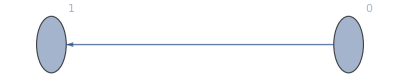

```mathematica
FAPlot[Regex["0"]]
```

El NFA que reconoce (0∪1)^* es

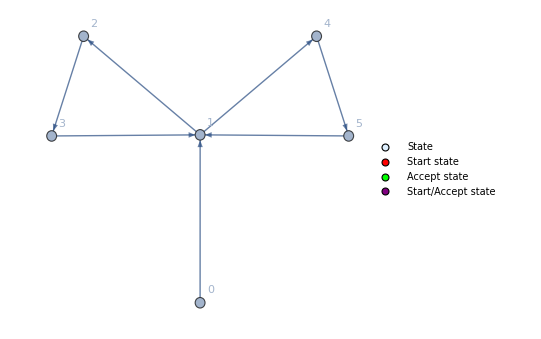

```mathematica
FAPlot[RegexStar[RegexAlphabet["01"]]]
```

Y el que reconoce 1 es

```mathematica
FAPlot[Regex["1"]]
```

-Graphics-

Al concatenar las tres expresiones regulares se obtiene el siguiente autómata

```mathematica
homeworkNFA = RegexConcatenation[Regex["0"],RegexStar[RegexAlphabet["01"]],Regex["1"]]
```

<|Name→0(0∪1)^*1,Type→NFA,Transitions→{<|Parent→0,Node→1,InputSymbol→{0}|>,<|Parent→4,Node→5,InputSymbol→{0}|>,<|Parent→6,Node→7,InputSymbol→{1}|>,<|Parent→3,Node→4,InputSymbol→ϵ|>,<|Parent→3,Node→6,InputSymbol→ϵ|>,<|Parent→2,Node→3,InputSymbol→ϵ|>,<|Parent→5,Node→3,InputSymbol→ϵ|>,<|Parent→7,Node→3,InputSymbol→ϵ|>,<|Parent→1,Node→2,InputSymbol→ϵ|>,<|Parent→8,Node→9,InputSymbol→{1}|>,<|Parent→5,Node→8,InputSymbol→ϵ|>,<|Parent→7,Node→8,InputSymbol→ϵ|>,<|Parent→2,Node→8,InputSymbol→ϵ|>},StartState→0,AcceptStates→{9},StateExpressions→{}|>

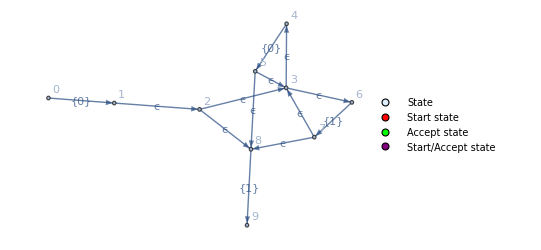

```mathematica
FAPlot[homeworkNFA,"Labeled"->True]
```

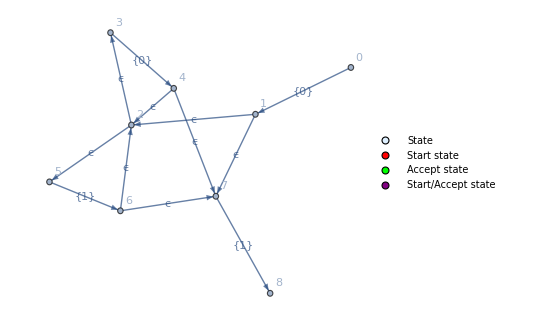

```mathematica
FAPlot[SimplifyMachine@homeworkNFA,"Labeled"->True]
```

```mathematica
RegexPlotExecution[homeworkNFA,"00101"]
```

```mathematica
RegexPlotExecution[SimplifyMachine@homeworkNFA,"00101"]
```

Es posible simplificar el autómata convirtiéndolo en su respectiva versión determinista.

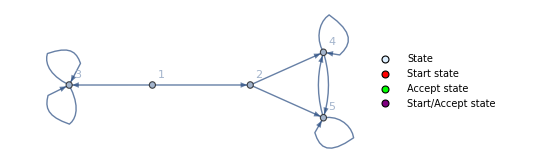

```mathematica
FAPlot[NFAToDFA[homeworkNFA]]
```

```mathematica
NFAPlotExecution[NFAToDFA[homeworkNFA],{"0","0","1","0","1"}]
```

```mathematica
NFAPlotExecution[NFAToDFA[homeworkNFA],{"1","1","0","1","1"}]
```

b)

A = {w | w empieza con 0 y termina con 1}
En Regex: 0(0∪1)^*1

```mathematica
A = SimplifyMachine@RegexConcatenation[Regex["0"],RegexStar[RegexAlphabet["01"]],Regex["1"]];
```

B = {w | w contiene al menos 3 unos}
En Regex: ""(0∪1)^*(111)^+(0∪1)^*"

```mathematica
B = SimplifyMachine@RegexConcatenation[RegexStar[RegexAlphabet["01"]],RegexDagger[Regex["111"]],RegexStar[RegexAlphabet["01"]]];
```

```mathematica
RegexPlotExecution[B,"111","SimpleNodes"->True]
```

Unir ambas máquinas da como resultado el siguiente autómata

```mathematica
automata = NFAToDFA[NFAUnion[A,B]]
```

<|Name→0(0∪1)^*1∪(0∪1)^*111(111)^*(0∪1)^*,Type→DFA,Transitions→{<|Parent→1,Node→2,InputSymbol→{0}|>,<|Parent→1,Node→3,InputSymbol→{1}|>,<|Parent→2,Node→4,InputSymbol→{0}|>,<|Parent→2,Node→5,InputSymbol→{1}|>,<|Parent→3,Node→6,InputSymbol→{0}|>,<|Parent→3,Node→7,InputSymbol→{1}|>,<|Parent→4,Node→4,InputSymbol→{0}|>,<|Parent→4,Node→5,InputSymbol→{1}|>,<|Parent→5,Node→4,InputSymbol→{0}|>,<|Parent→5,Node→8,InputSymbol→{1}|>,<|Parent→6,Node→6,InputSymbol→{0}|>,<|Parent→6,Node→3,InputSymbol→{1}|>,<|Parent→7,Node→6,InputSymbol→{0}|>,<|Parent→7,Node→9,InputSymbol→{1}|>,<|Parent→8,Node→4,InputSymbol→{0}|>,<|Parent→8,Node→10,InputSymbol→{1}|>,<|Parent→9,Node→11,InputSymbol→{0}|>,<|Parent→9,Node→12,InputSymbol→{1}|>,<|Parent→10,Node→13,InputSymbol→{0}|>,<|Parent→10,Node→14,InputSymbol→{1}|>,<|Parent→11,Node→11,InputSymbol→{0}|>,<|Parent→11,Node→15,InputSymbol→{1}|>,<|Parent→12,Node→11,InputSymbol→{0}|>,<|Parent→12,Node→16,InputSymbol→{1}|>,<|Parent→13,Node→13,InputSymbol→{0}|>,<|Parent→13,Node→17,InputSymbol→{1}|>,<|Parent→14,Node→13,InputSymbol→{0}|>,<|Parent→14,Node→18,InputSymbol→{1}|>,<|Parent→15,Node→11,InputSymbol→{0}|>,<|Parent→15,Node→19,InputSymbol→{1}|>,<|Parent→16,Node→11,InputSymbol→{0}|>,<|Parent→16,Node→20,InputSymbol→{1}|>,<|Parent→17,Node→13,InputSymbol→{0}|>,<|Parent→17,Node→21,InputSymbol→{1}|>,<|Parent→18,Node→13,InputSymbol→{0}|>,<|Parent→18,Node→22,InputSymbol→{1}|>,<|Parent→19,Node→11,InputSymbol→{0}|>,<|Parent→19,Node→23,InputSymbol→{1}|>,<|Parent→20,Node→11,InputSymbol→{0}|>,<|Parent→20,Node→20,InputSymbol→{1}|>,<|Parent→21,Node→13,InputSymbol→{0}|>,<|Parent→21,Node→24,InputSymbol→{1}|>,<|Parent→22,Node→13,InputSymbol→{0}|>,<|Parent→22,Node→22,InputSymbol→{1}|>,<|Parent→23,Node→11,InputSymbol→{0}|>,<|Parent→23,Node→12,InputSymbol→{1}|>,<|Parent→24,Node→13,InputSymbol→{0}|>,<|Parent→24,Node→14,InputSymbol→{1}|>},StartState→1,AcceptStates→{5,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},StateExpressions→{}|>

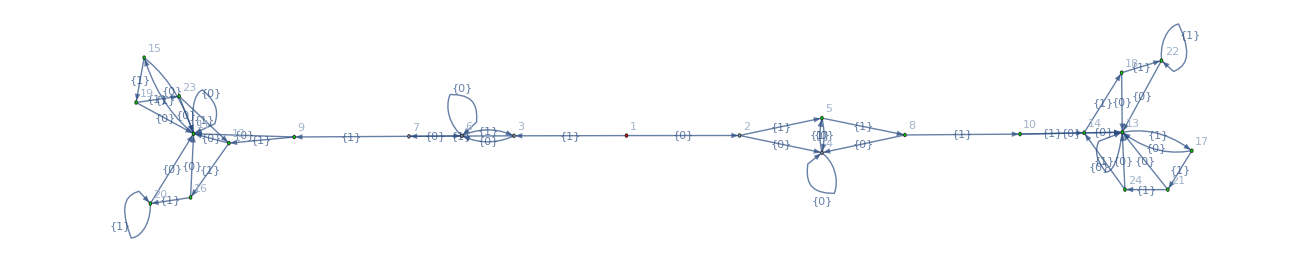

```mathematica
FAPlot[NFAToDFA[NFAUnion[A,B]],"Labeled"->True,"Legended"->False]
```

```mathematica
DFAPlotExecution[automata,{"0","0","1","0","1"},True]
```

```mathematica
RegexComputeTrace[automata,"00101"]
```

```mathematica
RegexComputeTrace[automata,"111"]
```

```mathematica
RegexComputeTrace[automata,"11"]
```